```mathematica
Clear["Global`*"]
```

Create n/n_0 curves for fixed ΔΦ, variable R_B

## Distribution funcs

```mathematica
vbthK[dPhi_,Tm_,kappa_]:=√(dPhi/(Tm(1-3/(2 kappa))));
vbth[dPhi_,Tm_]:=√(dPhi/Tm);
```

### Dist. funcs in Cartesian

```mathematica
MaxwellianArbPot[vpar_,vperp_,vbth_,alpha_]:=2/(√π)Exp[-(vperp^2+vpar^2-2 vbth(vpar^2+(1-alpha)vperp^2-vbth^2)^(1/2))]UnitStep[vpar]
```

```mathematica
KappaArbPot[vpar_,vperp_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vperp^2+vpar^2-2 vbth(vpar^2+(1-alpha)vperp^2-vbth^2)^(1/2))/(kappa-3/2))^(-(kappa+1))
```

```mathematica
MaxwellianArbPotUnitStep[vpar_,vperp_,vbth_,alpha_]:=1/π^(1/2)Exp[-(vperp^2+vpar^2-2 vbth(vpar^2+(1-alpha)vperp^2-vbth^2)^(1/2))]UnitStep[vpar^2+(1-alpha)vperp^2-vbth^2]
```

```mathematica
KappaArbPotUnitStep[vpar_,vperp_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(vperp^2+vpar^2-2 vbth(vpar^2+(1-alpha)vperp^2-vbth^2)^(1/2))/(kappa-3/2))^(-(kappa+1))UnitStep[vpar^2+(1-alpha)vperp^2-vbth^2]
```

### Dist. functions in cylindrical coordinates

```mathematica
MaxwellArbPotCyl[rho_,phi_,vbth_,alpha_]:=2/(√π)Exp[-(rho^2-2 vbth(rho^2(1-alpha (Sin[phi])^2)-vbth^2)^(1/2))];
MaxwellArbPotCylUnitStep[rho_,phi_,vbth_,alpha_]:=2/(√π)Exp[-(rho^2-2 vbth(rho^2(1-alpha (Sin[phi])^2)-vbth^2)^(1/2))]UnitStep[rho^2(1-alpha(Sin[phi])^2)-vbth^2];
```

```mathematica
KappaArbPotCyl[rho_,phi_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(rho^2-2 vbth(rho^2(1-alpha (Sin[phi])^2)-vbth^2)^(1/2))/(kappa-3/2))^(-(kappa+1))
```

```mathematica
KappaArbPotCylUnitStep[rho_,phi_,vbth_,alpha_,kappa_]:=2/(√π(1-3/(2kappa))^(3/2))Gamma[kappa+1]/(kappa^(3/2)Gamma[kappa-1/2])(1+(rho^2-2 vbth(rho^2(1-alpha (Sin[phi])^2)-vbth^2)^(1/2))/(kappa-3/2))^(-(kappa+1))UnitStep[rho^2(1-alpha(Sin[phi])^2)-vbth^2];
```

## Visualize

```mathematica
dPhi=941;Tm=110;
```

#### Parametric Maxwellian

```mathematica
Manipulate[ParametricPlot3D[{rho Cos[phi],rho Sin[phi],MaxwellArbPotCylUnitStep[rho,phi,vbth[dPhi,Tm],alpha]},{rho,0,6},{phi,-π/2,π/2},PlotRange->All,PlotPoints->20,ImageSize->800],{{alpha,1},0.001,1}]
```

```mathematica
Manipulate[ContourPlot[MaxwellianArbPot[vpar,vperp,vbth[dPhi,Tm],alpha],{vpar,0,8},{vperp,-4,4},ImageSize->600,PlotRange->Full],{{alpha,1},1,0.001}]
```

#### Parametric kappa

```mathematica
Manipulate[ContourPlot[KappaArbPot[vpar,vperp,vbth[dPhi,Tm],alpha,kappa],{vpar,0,8},{vperp,-4,4},ImageSize->600,PlotRange->Full,ColorFunction->GrayLevel],{{alpha,1},1,0.001},{{kappa,3},1.5,10}]
```

## Generate curves

```mathematica
dPhi=941;Tm=110;
```

```mathematica
minRhoInteg=0;maxRhoInteg=12;
```

```mathematica
alphaList={1,1/2,1/3,1/4,1/5,1/7,1/8,1/10,1/15,1/18,1/20,1/25,1/30,1/40,1/50,1/60,1/70,1/80,1/90,1/100,1/130,1/170,1/200,1/250,1/300,1/400,1/500,1/600,1/700,1/800,1/1000,1/1500,1/2000,1/3000};
```

```mathematica
RBList=1/alphaList
```

{1,2,3,4,5,7,8,10,15,18,20,25,30,40,50,60,70,80,90,100,130,170,200,250,300,400,500,600,700,800,1000,1500,2000,3000}

```mathematica
MaxwellIntegList = (NIntegrate[rho^2 Sin[phi] MaxwellArbPotCylUnitStep[rho,phi,vbth[dPhi,Tm],#],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@ alphaList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.69143,1.4275,2.23079,3.12638,4.09433,6.06769,7.00736,8.72201,12.0378,13.4996,14.3138,15.9373,17.1444,18.8104,19.9017,20.6703,21.2406,21.6802,22.0294,22.3135,22.917,23.4034,23.6449,23.9236,24.1087,24.3444,24.4872,24.5828,24.6515,24.703,24.7774,24.8724,24.9211,24.9698}

```mathematica
kappaEq1p6=(NIntegrate[rho^2 Sin[phi] KappaArbPotCylUnitStep[rho,phi,vbth[dPhi,Tm],#,16/10],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@alphaList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.700809,1.41741,2.1453,2.88214,3.62646,5.13327,5.89407,7.42722,11.3032,13.6434,15.2047,19.099,22.9641,30.5479,37.8758,44.9104,51.6357,58.0493,64.1576,69.969,85.7639,103.525,114.828,130.66,143.583,163.345,177.707,188.597,197.132,203.998,214.357,229.708,238.135,247.127}

```mathematica
kappaEq1p8=(NIntegrate[rho^2 Sin[phi] KappaArbPotCylUnitStep[rho,phi,vbth[dPhi,Tm],#,18/10],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@alphaList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.696264,1.42154,2.16912,2.93323,3.70977,5.28765,6.08405,7.6823,11.6466,13.9689,15.4845,19.1418,22.597,28.8928,34.4218,39.2782,43.558,47.3475,50.72,53.7368,61.1211,68.2619,72.2911,77.385,81.1355,86.2891,89.6596,92.035,93.7988,95.1603,97.1243,99.8535,101.268,102.717}

```mathematica
kappaEq2=(NIntegrate[rho^2 Sin[phi] KappaArbPotCylUnitStep[rho,phi,vbth[dPhi,Tm],#,2],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@alphaList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.694401,1.42438,2.18427,2.96595,3.76302,5.3831,6.19817,7.8236,11.7705,14.0162,15.4536,18.8301,21.9027,27.2257,31.6267,35.3031,38.4077,41.0585,43.3465,45.3353,50.0045,54.2693,56.5767,59.3984,61.4138,64.0993,65.8066,66.9876,67.853,68.5143,69.4585,70.7517,71.4134,72.0854}

```mathematica
kappaEq3=(NIntegrate[rho^2 Sin[phi] KappaArbPotCylUnitStep[rho,phi,vbth[dPhi,Tm],#,3],{rho,minRhoInteg,maxRhoInteg},{phi,0,π/2}])&/@alphaList
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{0.692098,1.42921,2.21703,3.04455,3.89739,5.62787,6.48592,8.15572,11.9283,13.8906,15.0802,17.6877,19.8563,23.2228,25.696,27.5813,29.0627,30.2561,31.2374,32.058,33.8717,35.4064,36.1933,37.1204,37.7542,38.5732,39.0776,39.4194,39.6664,39.8531,40.1168,40.4725,40.6522,40.833}

```mathematica
MaxwellPlotList=Partition[Riffle[RBList,MaxwellIntegList],2]
```

{{1,0.69143},{2,1.4275},{3,2.23079},{4,3.12638},{5,4.09433},{7,6.06769},{8,7.00736},{10,8.72201},{15,12.0378},{18,13.4996},{20,14.3138},{25,15.9373},{30,17.1444},{40,18.8104},{50,19.9017},{60,20.6703},{70,21.2406},{80,21.6802},{90,22.0294},{100,22.3135},{130,22.917},{170,23.4034},{200,23.6449},{250,23.9236},{300,24.1087},{400,24.3444},{500,24.4872},{600,24.5828},{700,24.6515},{800,24.703},{1000,24.7774},{1500,24.8724},{2000,24.9211},{3000,24.9698}}

```mathematica
kappaEq1p6PlotList=Partition[Riffle[RBList,kappaEq1p6],2]
```

{{1,0.700809},{2,1.41741},{3,2.1453},{4,2.88214},{5,3.62646},{7,5.13327},{8,5.89407},{10,7.42722},{15,11.3032},{18,13.6434},{20,15.2047},{25,19.099},{30,22.9641},{40,30.5479},{50,37.8758},{60,44.9104},{70,51.6357},{80,58.0493},{90,64.1576},{100,69.969},{130,85.7639},{170,103.525},{200,114.828},{250,130.66},{300,143.583},{400,163.345},{500,177.707},{600,188.597},{700,197.132},{800,203.998},{1000,214.357},{1500,229.708},{2000,238.135},{3000,247.127}}

```mathematica
kappaEq1p8PlotList=Partition[Riffle[RBList,kappaEq1p8],2]
```

{{1,0.696264},{2,1.42154},{3,2.16912},{4,2.93323},{5,3.70977},{7,5.28765},{8,6.08405},{10,7.6823},{15,11.6466},{18,13.9689},{20,15.4845},{25,19.1418},{30,22.597},{40,28.8928},{50,34.4218},{60,39.2782},{70,43.558},{80,47.3475},{90,50.72},{100,53.7368},{130,61.1211},{170,68.2619},{200,72.2911},{250,77.385},{300,81.1355},{400,86.2891},{500,89.6596},{600,92.035},{700,93.7988},{800,95.1603},{1000,97.1243},{1500,99.8535},{2000,101.268},{3000,102.717}}

```mathematica
kappaEq2PlotList=Partition[Riffle[RBList,kappaEq2],2]
```

{{1,0.694401},{2,1.42438},{3,2.18427},{4,2.96595},{5,3.76302},{7,5.3831},{8,6.19817},{10,7.8236},{15,11.7705},{18,14.0162},{20,15.4536},{25,18.8301},{30,21.9027},{40,27.2257},{50,31.6267},{60,35.3031},{70,38.4077},{80,41.0585},{90,43.3465},{100,45.3353},{130,50.0045},{170,54.2693},{200,56.5767},{250,59.3984},{300,61.4138},{400,64.0993},{500,65.8066},{600,66.9876},{700,67.853},{800,68.5143},{1000,69.4585},{1500,70.7517},{2000,71.4134},{3000,72.0854}}

```mathematica
kappaEq3PlotList=Partition[Riffle[RBList,kappaEq3],2]
```

{{1,0.692098},{2,1.42921},{3,2.21703},{4,3.04455},{5,3.89739},{7,5.62787},{8,6.48592},{10,8.15572},{15,11.9283},{18,13.8906},{20,15.0802},{25,17.6877},{30,19.8563},{40,23.2228},{50,25.696},{60,27.5813},{70,29.0627},{80,30.2561},{90,31.2374},{100,32.058},{130,33.8717},{170,35.4064},{200,36.1933},{250,37.1204},{300,37.7542},{400,38.5732},{500,39.0776},{600,39.4194},{700,39.6664},{800,39.8531},{1000,40.1168},{1500,40.4725},{2000,40.6522},{3000,40.833}}

### Plots of ze results

```mathematica
nDigitsdPhi=3;nDigitsTm=3;
```

```mathematica
zeroPoint5Line={{1,0.5},{10,0.5},{50,0.5},{100,0.5},{3000,0.5}};
```

#### Full range

```mathematica
legendStyles=(Style[#,18])&/@{"κ = 1.6","κ = 1.8","κ = 2","κ = 3","Maxwellian","n/n_0=0.5"}
```

{κ = 1.6,κ = 1.8,κ = 2,κ = 3,Maxwellian,n/n_0=0.5}

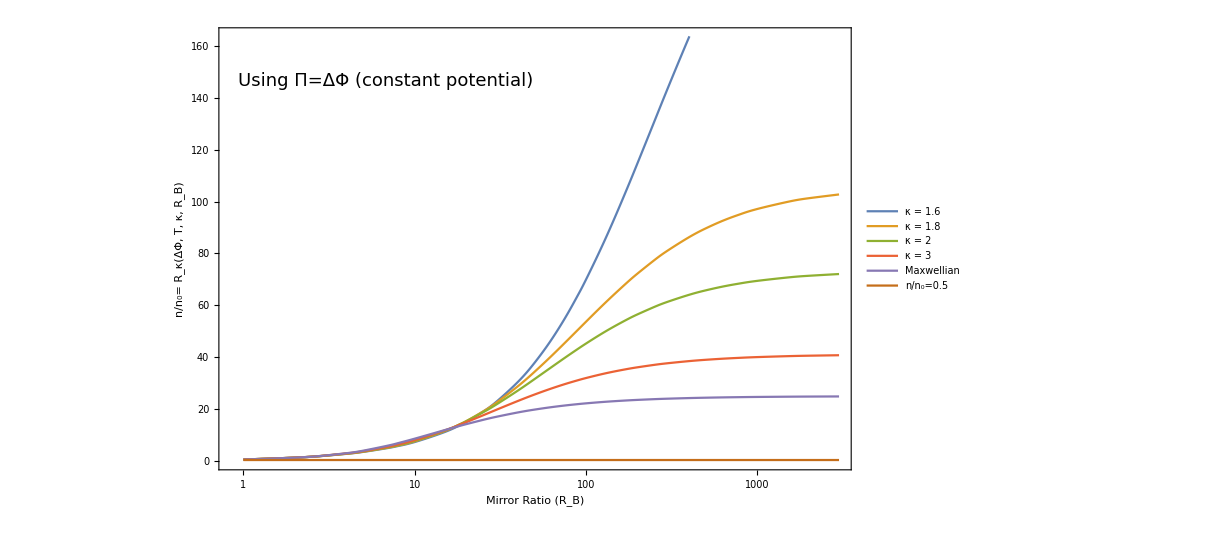

```mathematica
ListLogLinearPlot[{kappaEq1p6PlotList,kappaEq1p8PlotList,kappaEq2PlotList,kappaEq3PlotList,MaxwellPlotList,zeroPoint5Line},Joined->True,InterpolationOrder->3,PlotLegends->legendStyles,Frame->True,FrameStyle->Directive[Black,(FontSize->19)],PlotStyle->Directive[(FontSize->19)],FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio (R_B)"],StringForm["ΔΦ = `1` V; T_m = `2` eV; ϕ̄ = `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[Tm,nDigitsTm],NumberForm[N[dPhi/Tm],{3,1}]]}},Epilog->{Text[Style["Using Π=ΔΦ (constant potential)",18],Scaled[{0.03,0.9}],{-1,1}]},ImageSize->900]
```

#### Adjusted range

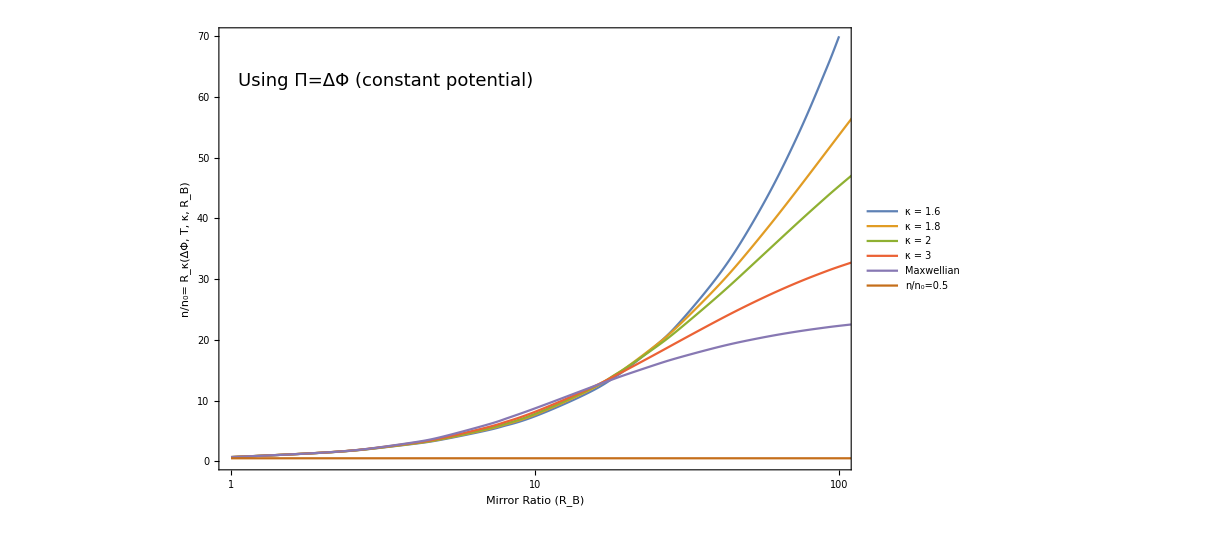

```mathematica
ListLogLinearPlot[{kappaEq1p6PlotList,kappaEq1p8PlotList,kappaEq2PlotList,kappaEq3PlotList,MaxwellPlotList,zeroPoint5Line},PlotRange->{{1,100},{0,70}},Joined->True,InterpolationOrder->3,PlotLegends->legendStyles,Frame->True,FrameStyle->Directive[Black,(FontSize->19)],PlotStyle->Directive[(FontSize->19)],FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio (R_B)"],StringForm["ΔΦ = `1` V; T_m = `2` eV; ϕ̄ = `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[Tm,nDigitsTm],NumberForm[N[dPhi/Tm],{3,1}]]}},Epilog->{Text[Style["Using Π=ΔΦ (constant potential)",18],Scaled[{0.03,0.9}],{-1,1}]},ImageSize->900]
```

## Compare these curves with what we get analytically

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
```

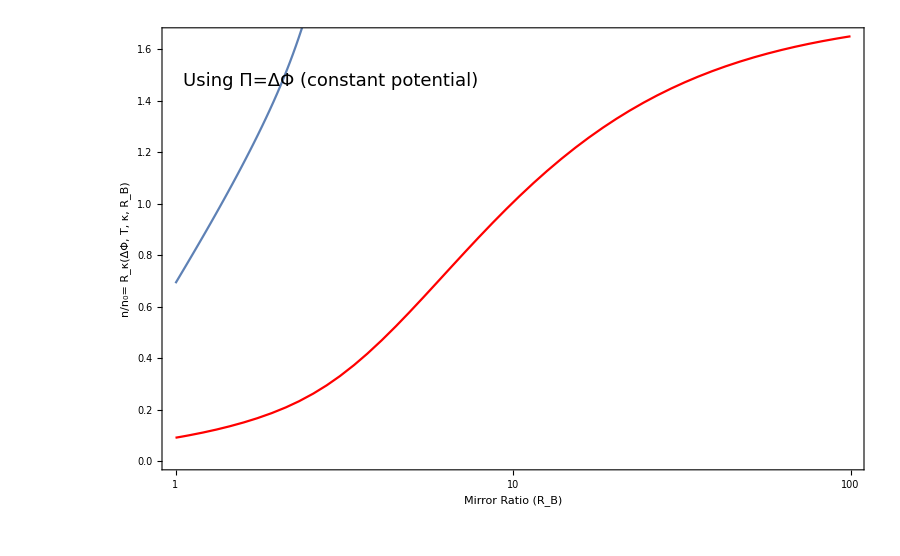

```mathematica
Show[{LogLinearPlot[LKMwellDensFac[dPhi/Tm,RB],{RB,1,100},Frame->True,FrameStyle->Directive[Black,(FontSize->19)],PlotStyle->Directive[Red,(FontSize->19)],FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio (R_B)"],StringForm["ΔΦ = `1` V; T_m = `2` eV; ϕ̄ = `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[Tm,nDigitsTm],NumberForm[N[dPhi/Tm],{3,1}]]}},Epilog->{Text[Style["Using Π=ΔΦ (constant potential)",18],Scaled[{0.03,0.9}],{-1,1}]},ImageSize->900],ListLogLinearPlot[MaxwellPlotList,PlotRange->{{1,100},{0,70}},Joined->True,InterpolationOrder->3,Frame->True,FrameStyle->Directive[Black,(FontSize->19)],PlotStyle->Directive[(FontSize->19)],FrameLabel->{{StringForm["n/n_0= R_κ(ΔΦ, T, κ, R_B)"],""},{StringForm["Mirror Ratio (R_B)"],StringForm["ΔΦ = `1` V; T_m = `2` eV; ϕ̄ = `3`",NumberForm[dPhi,nDigitsdPhi],NumberForm[Tm,nDigitsTm],NumberForm[N[dPhi/Tm],{3,1}]]}},Epilog->{Text[Style["Using Π=ΔΦ (constant potential)",18],Scaled[{0.03,0.9}],{-1,1}]},ImageSize->900]}]
```